```mathematica
(*x , y , g(x , y) -> x' , y' , f(x' , y')*)
```

```mathematica
xx[{x_ , y_}]:=0.5 x + 2.0 y;
```

```mathematica
yy[{x_ , y_}]:=0.2 x^2 - 0.5 Sin[2y];
```

```mathematica
pointsxy = Flatten[Table[{x , y} , {x , 0.2 , 0.7 , 0.02} , {y , -1.0 , -0.5 , 0.02}] , 1];
```

```mathematica
pointsxxyy = Transpose[{xx/@pointsxy , yy/@pointsxy}];
```

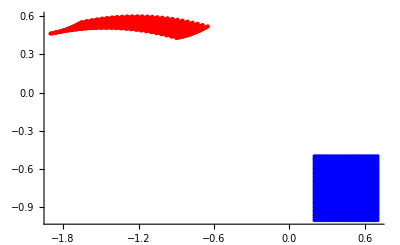

```mathematica
Graphics[{PointSize[Tiny],{{Blue , Point/@pointsxy} , {Red , Point/@pointsxxyy}}} , Axes->True , PlotRange->All]
```

```mathematica
Manipulate[Graphics[
{PointSize[Tiny],
{
{Blue , Point/@pointsxy} , 
{Red , Point/@pointsxxyy},
{Opacity[0.5] , Gray  , Point/@(t pointsxxyy + (1 - t) pointsxy)}
}
} , Axes->True , PlotRange->All] , {t , 0 , 1}]
```